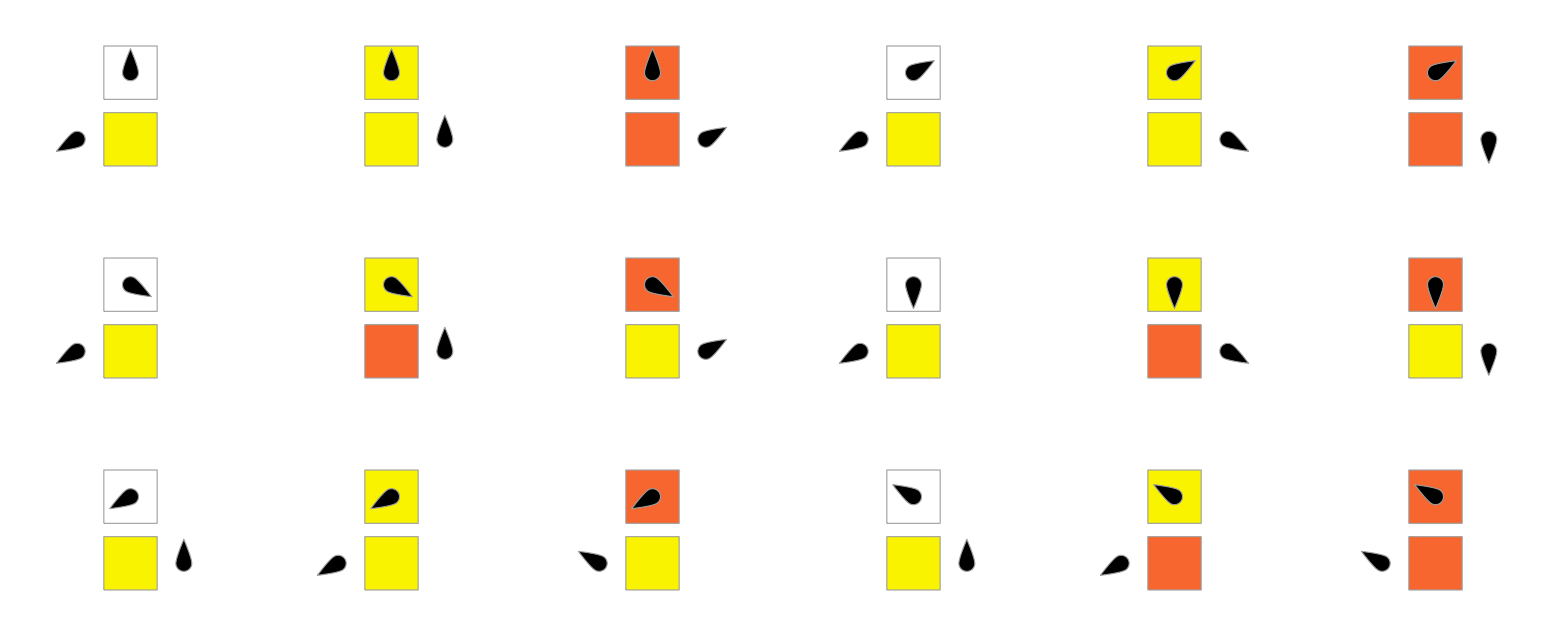
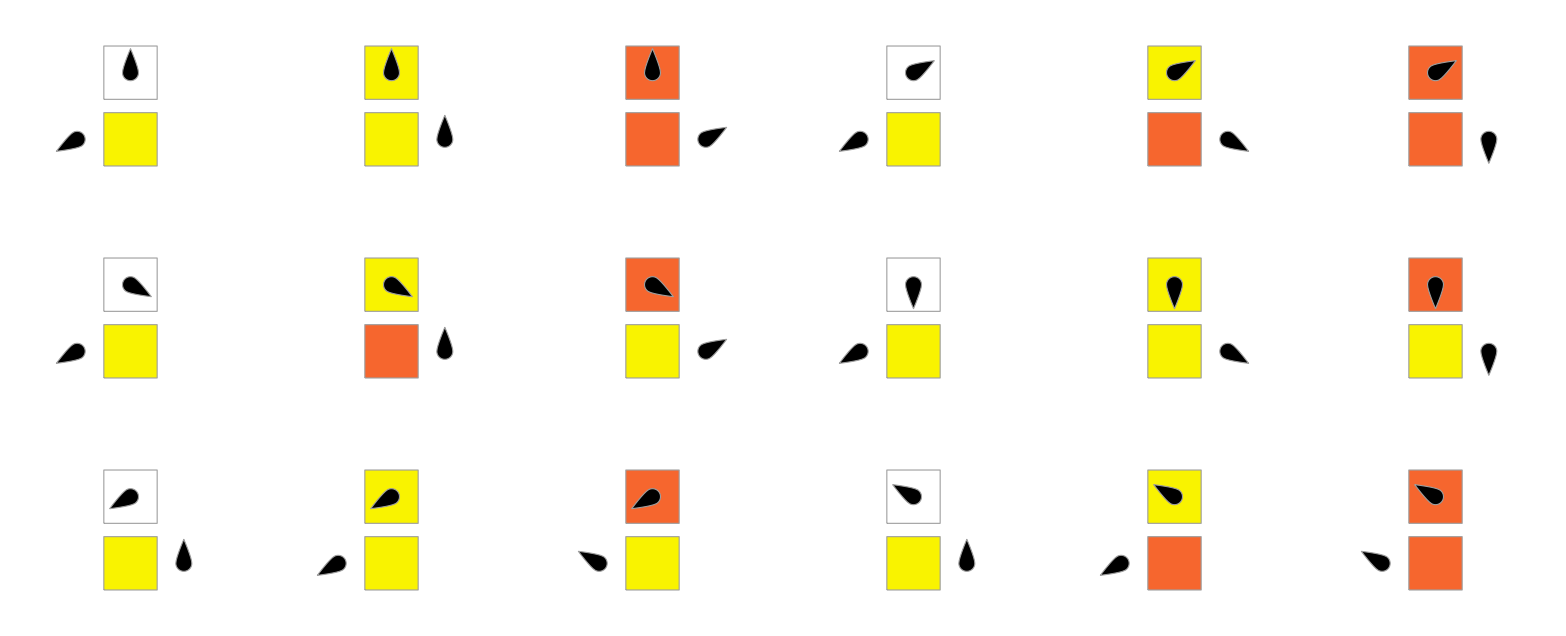

```mathematica
CAToTM[rule_]:=With[{sts={q[0,0]->1,q[0,1]->2,q[1,0]->3,q[1,1]->4,p[0]->5,p[1]->6}},#->(#/.{{q[a_,b_],c:0|1}:>{q[b,c],CellularAutomaton[rule,{a,b,c}][[2]],1},{q[_,_],x}->{p[0],0,-1},{p[a_],b:0|1}->{p[b],a,-1},{p[_],x}->{q[0,0],0,1}})&/@Tuples[{Keys[sts],{x,0,1}}]/.sts/.({a_,b_}->{c_,d_,e_}):>{a,b/.{x->0,0->1,1->2}}->{c,d+1,e}];

RulePlot[TuringMachine[CAToTM[#]]]&/@{90,30}
```